```mathematica
ClearAll[β,h0,x,y,z,HBx,HBy,HBz,q,H,eigH,Z,F]
Needs["NumericalCalculus`"]
h0=({{0, -1, -1, 0, -1, -1}, {-1, 0, -1, -1, 0, -1}, {-1, -1, 0, -1, -1, 0}, {0, -1, -1, 0, -1, -1}, {-1, 0, -1, -1, 0, -1}, {-1, -1, 0, -1, -1, 0}});
x=DiagonalMatrix[{1,0,0,-1,0,0}];
y=DiagonalMatrix[{0,1,0,0,-1,0}];
z=DiagonalMatrix[{0,0,1,0,0,-1}];
HBx=1/2(TensorProduct[{0,1,-I,0,-1,I},{0,1,I,0,-1,-I}]-TensorProduct[{0,1,I,0,-1,-I},{0,1,-I,0,-1,I}]);
HBy=1/2(TensorProduct[{1,0,-I,-1,0,I},{1,0,I,-1,0,-I}]-TensorProduct[{1,0,I,-1,0,-I},{1,0,-I,-1,0,I}]);
HBz=1/2(TensorProduct[{1,-I,0,-1,I,0},{1,I,0,-1,-I,0}]-TensorProduct[{1,I,0,-1,-I,0},{1,-I,0,-1,I,0}]);
H[Ox_,Oz_,Bx_,Bz_]:=h0+Bx*HBx+Bz*HBz-Ox*x-Oz*z+1/2(Ox^2+Oz^2)*IdentityMatrix[6];
F[β_,Ox_,Oz_,Bx_,Bz_]:=-1/β Log[Sum[Exp[-β*Eigenvalues[H[Ox,Oz,Bx,Bz]][[i]]],{i,1,6}]]
```

## Analytic Derivatives

```mathematica
ClearAll[Fx2,FxBx,FB2,Fx4,Fx2Bx2,FB4]
(*Quadratic*)
(*Ox^2*)
Fx2[β_]:=Simplify[D[F[β,Ox,0,0,0],{Ox,2}]/.{Ox->0}]
(*Ox Bx*)
FxBx[β_]:=Simplify[D[F[β,Ox,0,Bx,0],{Ox,1},{Bx,1}]/.{Ox->0,Bx->0} ]
(*Bx^2*)
FB2[β_]:=Simplify[D[F[β,0,0,Bx,0],{Bx,2}]/.{Bx->0}] 
(*Quartic*)
(*Ox^4*)
Fx4[β_]:=Simplify[D[F[β,Ox,0,0,0],{Ox,4}]/.{Ox->0}]
(*Ox^2 Oz^2 Doesn't work -- Indeterminate *)
(*Ox^2 Bx^2*)
Fx2Bx2[β_]:=Simplify[D[F[β,Ox,0,Bx,0],{Ox,2},{Bx,2}]/.{Ox->0,Bx->0} ]
(*Ox^2 Bz^2 Doesn't work -- Indeterminate *)
(*Bx^4*)
FB4[β_]:=Simplify[D[F[β,0,0,Bx,0],{Bx,4}]/.{Bx->0}] 
(*Ox Bx Oz Bz Doesn't work -- Indeterminate*)
```

## Numerical Derivatives

```mathematica
ClearAll[Fnum,FOx2Bz2num,FOx2Bz2num1,FOx2Bz2num,FOxBxOzBznum1,FOxBxOzBznum2,FOxBxOzBznum3,FOxBxOzBznum]
(*Free Energy*)
Fnum[β_?NumericQ,Ox_?NumericQ,Oz_?NumericQ,Bx_?NumericQ,Bz_?NumericQ]:=-1/β Log[Sum[Exp[-β*Eigenvalues[H[Ox,Oz,Bx,Bz]][[i]]],{i,1,6}]]
(*Ox^2 Bz^2*)
FOx2Bz2num1[β_?NumericQ,Ox_?NumericQ,Bz_?NumericQ]:=ND[Fnum[β,a,0,0,Bz],{a,2},Ox]
FOx2Bz2num[β_?NumericQ,Ox_?NumericQ,Bz_?NumericQ]:=ND[FOx2Bz2num1[β,Ox,b],{b,2},Bz]
(*Ox^2 Oz^2*)
FOx2Oz2num1[β_?NumericQ,Ox_?NumericQ,Oz_?NumericQ]:=ND[Fnum[β,a,Oz,0,0],{a,2},Ox]
FOx2Oz2num[β_?NumericQ,Ox_?NumericQ,Oz_?NumericQ]:=ND[FOx2Bz2num1[β,Ox,b],{b,2},Oz]
(*OxBxOzBz*)
FOxBxOzBznum1[β_?NumericQ,Ox_?NumericQ,Oz_?NumericQ,Bx_?NumericQ,Bz_?NumericQ]:=ND[Fnum[β,a,Oz,Bx,Bz],a,Ox]
FOxBxOzBznum2[β_?NumericQ,Ox_?NumericQ,Oz_?NumericQ,Bx_?NumericQ,Bz_?NumericQ]:=ND[FOxBxOzBznum1[β,Ox,b,Bx,Bz],b,Oz]
FOxBxOzBznum3[β_?NumericQ,Ox_?NumericQ,Oz_?NumericQ,Bx_?NumericQ,Bz_?NumericQ]:=ND[FOxBxOzBznum2[β,Ox,Oz,c,Bz],c,Bx]
FOxBxOzBznum[β_?NumericQ,Ox_?NumericQ,Oz_?NumericQ,Bx_?NumericQ,Bz_?NumericQ]:=ND[FOxBxOzBznum3[β,Ox,Oz,Bx,d],d,Bz]
(*Eigenvalues*)
g[a_?NumericQ,b_?NumericQ,c_?NumericQ,d_?NumericQ]:=Sort[Eigenvalues[H[a,b,c,d]]]
g1[a_?NumericQ,b_?NumericQ,c_?NumericQ,d_?NumericQ]:=ND[g[a1,b,c,d],a1,a]
g2[a_?NumericQ,b_?NumericQ,c_?NumericQ,d_?NumericQ]:=ND[g1[a,b1,c,d],b1,b]
g3[a_?NumericQ,b_?NumericQ,c_?NumericQ,d_?NumericQ]:=ND[g2[a,b,c1,d],c1,c]
g4[a_?NumericQ,b_?NumericQ,c_?NumericQ,d_?NumericQ]:=ND[g3[a,b,c,d1],d1,d]
```

## Free Energy Approximation

```mathematica
Fapprox[β_?NumericQ,Ox_,Oz_,Bx_,Bz_,Ox2Oz2coef_,Ox2Bz2coef_,OxOzBxBzcoef_]:=F[β,0,0,0,0]+1/(2!)((16+15 ⅇ^(2 β)+5 ⅇ^(6 β))/(6 (2+3 ⅇ^(2 β)+ⅇ^(6 β)))*(Ox^2+Oz^2)-(8 β)/(3+2 ⅇ^(-2 β)+ⅇ^(4 β))*(Bx^2+Bz^2))+1/(4!)(-(ⅇ^(12 β)+32 (5+3 β)+27 ⅇ^(4 β) (-9+4 β)+6 ⅇ^(8 β) (-13+6 β)+2 ⅇ^(6 β) (41+78 β)+6 ⅇ^(2 β) (13+90 β))/(72 (2+3 ⅇ^(2 β)+ⅇ^(6 β))^2)*(Ox^4+Oz^4)+6*Ox2Oz2coef*Ox^2 Oz^2+6*(4 ⅇ^(2 β) (-4+3 ⅇ^(2 β)+ⅇ^(6 β)) β^2)/(3 (2+3 ⅇ^(2 β)+ⅇ^(6 β))^2)*(Ox^2 Bx^2+Oz^2 Bz^2)+6*Ox2Bz2coef*(Ox^2 Bz^2+Oz^2 Bx^2)+4*OxOzBxBzcoef*Ox*Oz*Bx*Bz-(32 ⅇ^(2 β) (-1+ⅇ^(2 β))^2 (2+ⅇ^(2 β)) β^3)/((2+3 ⅇ^(2 β)+ⅇ^(6 β))^2)*(Bx^4+Bz^4))
```

## Plots

### Derivatives as function of temperature

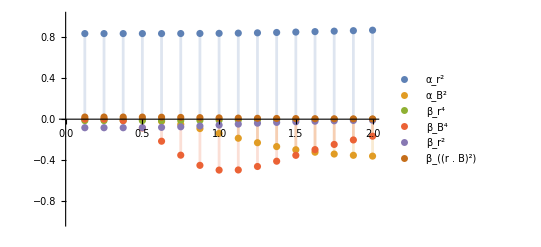

```mathematica
DiscretePlot[{Fx2[1/T],FB2[1/T],Fx4[1/T],FB4[1/T],FOx2Bz2num[1/T,0,0],1/2 FOxBxOzBznum[1/T,0,0,0,0]},{T,0,2,.125},PlotLegends->{"α_(r^2)","α_(B^2)","β_(r^4)","β_(B^4)","β_(r^2)","β_((r . B)^2)"},PlotRange->{-1,1}]
```

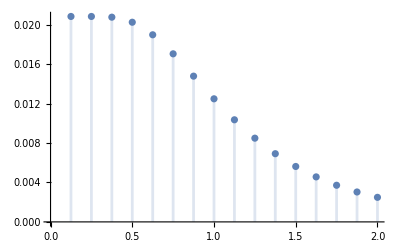

```mathematica
DiscretePlot[1/2 FOxBxOzBznum[1/T,0,0,0,0],{T,0,2,.125}]
```

```mathematica
1/2 FOxBxOzBznum[1/(.1),0,0,0,0]
```

0.0208294